```mathematica
ψ=ArcTan[-Bϕ/(√(Br^2+Bθ^2))]//.Bθ->0;
ζ=ArcTan[Bθ/Br]//.Bθ->0;
```

```mathematica
Sin[ζ]
```

0

```mathematica
Cos[ζ]
```

1

```mathematica
krr=FullSimplify[kperp Sin[ζ]^2+Cos[ζ]^2(kpar Cos[ψ]^2+kperp Sin[ψ]^2)]
(*krθ=FullSimplify[Sin[ζ]Cos[ζ](kpar Cos[ψ]^2+kperp Sin[ψ]^2-kperp)]*)
krϕ=FullSimplify[-(kpar-kperp)Sin[ψ]Cos[ψ]Cos[ζ]]
(*kθr=FullSimplify[Sin[ζ]Cos[ζ](kpar Cos[ψ]^2+kperp Sin[ψ]^2-kperp)]*)
kθθ=FullSimplify[kperp Cos[ζ]^2+Sin[ζ]^2(kpar Cos[ψ]^2+kperp Sin[ψ]^2)]
(*kθϕ=FullSimplify[-(kpar-kperp)Sin[ψ]Cos[ψ]Sin[ζ]]*)
kϕr=FullSimplify[-(kpar-kperp)Sin[ψ]Cos[ψ]Cos[ζ]]
(*kϕθ=FullSimplify[-(kpar-kperp)Sin[ψ]Cos[ψ]Sin[ζ]]*)
kϕϕ=FullSimplify[kpar Sin[ψ]^2+kperp Cos[ψ]^2]
```

(Br^2 kpar+Bϕ^2 kperp)/(Br^2+Bϕ^2)

(√(Br^2) Bϕ (kpar-kperp))/(Br^2+Bϕ^2)

kperp

(√(Br^2) Bϕ (kpar-kperp))/(Br^2+Bϕ^2)

(Br^2 kperp+Bϕ^2 kpar)/(Br^2+Bϕ^2)

```mathematica
krr=FullSimplify[kpar Cos[ψ]^2+kperp Sin[ψ]^2]
krϕ=FullSimplify[-(kpar-kperp)Sin[ψ]Cos[ψ]]
kθθ=kperp 
kϕr=FullSimplify[-(kpar-kperp)Sin[ψ]Cos[ψ]]
kϕϕ=FullSimplify[kpar Sin[ψ]^2+kperp Cos[ψ]^2]
```

(Br^2 kpar+Bϕ^2 kperp)/(Br^2+Bϕ^2)

(√(Br^2) Bϕ (kpar-kperp))/(Br^2+Bϕ^2)

kperp

(√(Br^2) Bϕ (kpar-kperp))/(Br^2+Bϕ^2)

(Br^2 kperp+Bϕ^2 kpar)/(Br^2+Bϕ^2)

```mathematica
bField={Ac*b0*(r0/r)^2,0,-Ac*b0*(r0/r)^2*(r-rSun)*Sin[th]*Omega/Vsw};
```

```mathematica
FullSimplify[Sqrt[bField.bField]]
```

```mathematica
√(Omega^2 (r-rSun)^2 sin^2(th)+Vsw^2)
```

```mathematica
b0/Vsw*(r0/r)^2 Sqrt[Omega^2(r-rSun)^2 Sin[th]^2+Vsw^2]
```

```mathematica
Sqrt[1/(4π)NIntegrate[(1/2 √(3/(2π))Sin[θ])^2 2π Sin[θ],{θ,0,π}]-(1/(4π)NIntegrate[1/2 √(3/(2π))Sin[θ]2π Sin[θ],{θ,0,π}])^2]
```

0.0771129

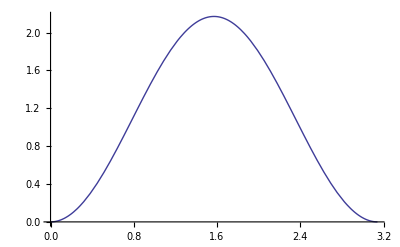

```mathematica
Plot[2π 1/2 √(3/(2π))Sin[θ]Sin[θ],{θ,0,π}]
```

```mathematica
μ=1/(4π)NIntegrate[1/2 √(3/(2π))Sin[θ]Sin[θ],{θ,0,π},{ϕ,0,2π}]
```

```mathematica
3*Sqrt[1/(4π)NIntegrate[(1/2 √(3/(2π))Sin[θ])^2 Sin[θ],{θ,0,π},{ϕ,0,2π}]-μ^2]
```

0.231339

```mathematica
Sqrt[3*(3*Sqrt[1/(4π)NIntegrate[(1/2 √(3/(2π))Sin[θ])^2 Sin[θ],{θ,0,π},{ϕ,0,2π}]-μ^2])^2]
```

0.40069

```mathematica
N[1/2 √(3/(2π))]
```

0.345494